# Triangle

### Author

Eric W. Weisstein
October 22, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/Triangles/Triangle.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/Triangle.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Figure

#### V5

```mathematica
t=Triangle[{{0,0},{1,0},{.3,.7}}];
Show[Graphics[{
t,
PointLabels[
Transpose[{VertexPoints[t],{"A","B","C"}}],
PointSize[.025],LabelOffset->.04
]
}],AspectRatio->Automatic,PlotRange->All]
```

⁃Graphics⁃

#### V6

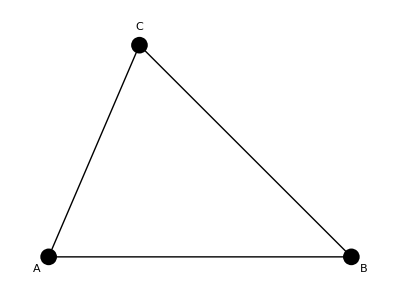

```mathematica
t=Triangle[{{0,0},{1,0},{.3,.7}}];
Graphics[{
t,
PointLabels[
Transpose[{{"A","B","C"},VertexPoints[t],{LabelOffset->-.04,LabelOffset->.04{1,-1},LabelOffset->.06{0,1}}}]
]}]
```

## Special Named Triangles

```mathematica
Triangles
```

{AnticomplementaryTriangle,BCITriangle,CircumcircleMidArcTriangle,CircumMedialTriangle,CircumnormalTriangle,CircumOrthicTriangle,CircumtangentialTriangle,ContactTriangle,DTriangle,EulerGergonneSoddyTriangle,EulerTriangle,ExcentralTriangle,ExtangentsTriangle,ExtouchTriangle,FeuerbachTriangle,FuhrmannTriangle,HalfAltitudeTriangle,HexylTriangle,IncentralTriangle,InnerNapoleonTriangle,InnerVectenTriangle,IntangentsTriangle,JohnsonTriangle,LemoineTriangle,LucasCentralTriangle,LucasInnerTriangle,LucasTangentsTriangle,MacBeathTriangle,MedialTriangle,MidArcTriangle,MixtilinearTriangle,OrthicTriangle,OuterNapoleonTriangle,OuterVectenTriangle,ReferenceTriangle,ReflectionTriangle,StammlerTriangle,SteinerTriangle,SymmedialTriangle,TangentialMidArcTriangle,TangentialTriangle,YffCentralTriangle,YffContactTriangle,YiuTriangle,BrocardTriangle[1],BrocardTriangle[2],BrocardTriangle[3],InscribedSquaresTriangle[1],InscribedSquaresTriangle[2],MorleyAdjunctTriangle[1],MorleyAdjunctTriangle[2],MorleyAdjunctTriangle[3],MorleyTriangle[1],MorleyTriangle[2],MorleyTriangle[3],NeubergTriangle[1],NeubergTriangle[2],YffCirclesTriangle[1],YffCirclesTriangle[2],YffTriangle[1],YffTriangle[2]}

## Semiperimeter Identity

```mathematica
s=(a+b+c)/2;
```

```mathematica
FullSimplify[s-b-(a-b+c)/2]
```

0

## Top Vertex Position in Terms of Sides

```mathematica
soln={x,y}/.FullSimplify[Solve[{x^2+y^2==b^2,(x-c)^2+y^2==a^2},{x,y}]]
```

{{(-a^2+b^2+c^2)/(2 c),-√(b^2-((-a^2+b^2+c^2)^2)/(4 c^2))},{(-a^2+b^2+c^2)/(2 c),√(b^2-((-a^2+b^2+c^2)^2)/(4 c^2))}}

```mathematica
FullSimplify[Together[b^2-((-a^2+b^2+c^2)^2)/(4 c^2)]]
```

-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/(4 c^2)

```mathematica
Factor//@Together//@soln
```

{{(-a^2+b^2+c^2)/(2 c),-1/2 √(-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/c^2)},{(-a^2+b^2+c^2)/(2 c),1/2 √(-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/c^2)}}

```mathematica
Simplify[ToAngles[%],TriangleQ[]&&Area>0]
```

{{b Cos[A],-(2 Area)/c},{b Cos[A],(2 Area)/c}}

```mathematica
Show[Graphics[Triangle[3,4,5]],AspectRatio->Automatic]
```

⁃Graphics⁃

## Sum of interior Angles = π

```mathematica
cos[α]=(b^2+c^2-a^2)/(2b c);
cos[β]=(-b^2+c^2+a^2)/(2c a);
cos[γ]=(-c^2+a^2+b^2)/(2a b);
```

```mathematica
Simplify[PowerExpand[Together//@(TrigExpand[Cos[α+β+γ]]/.{Cos[x_]:>cos[x],Sin[x_]:>Sqrt[1-cos[x]^2]})]]
```

-1

```mathematica
ArcCos[%]
```

π

## Angles in term of Side Lengths

```mathematica
Factor[Simplify[Together//@ToSidelengths[TrigExpand[Cos[#]]],TriangleQ[]]]&/@{A-B,B-C,C-A}
```

{-(a^4-2 a^2 b^2+b^4-a^2 c^2-b^2 c^2)/(2 a b c^2),(a^2 b^2-b^4+a^2 c^2+2 b^2 c^2-c^4)/(2 a^2 b c),-(a^4-a^2 b^2-2 a^2 c^2-b^2 c^2+c^4)/(2 a b^2 c)}

```mathematica
InputForm[%]
```

{-(a^4 - 2*a^2*b^2 + b^4 - a^2*c^2 - b^2*c^2)/(2*a*b*c^2), 
 (a^2*b^2 - b^4 + a^2*c^2 + 2*b^2*c^2 - c^4)/(2*a^2*b*c), 
 -(a^4 - a^2*b^2 - 2*a^2*c^2 - b^2*c^2 + c^4)/(2*a*b^2*c)}

## Identities

```mathematica
TriangleQ[]
```

a>0&&b>0&&c>0&&a+b>c&&b+c>a&&a+c>b&&A+B+C==π&&0<A<π&&0<B<π&&0<C<π

### cos(n A)-cos(n (B+C))

```mathematica
FullSimplify[1/8 (Cos[4 A]-Cos[4 (B+C)]),A+B+C==Pi]
```

1/8 (Cos[4 A]-Cos[4 (B+C)])

```mathematica
FullSimplify[(Cos[2 A]-Cos[2 (B+C)])/.C->Pi-(A+B)]
```

0

```mathematica
FullSimplify[(Cos[4 A]-Cos[4 (B+C)])/.C->Pi-(A+B)]
```

0

```mathematica
FullSimplify[(Cos[6A]-Cos[6(B+C)])/.C->Pi-(A+B)]
```

0

### -cos^2(B)-cos^2(C)+1==cos^2(A)+2 cos(B) cos(C) cos(A)

```mathematica
FullSimplify[Subtract@@{1-Cos[B]^2-Cos[C]^2,Cos[A]^2+2 Cos[A] Cos[B] Cos[C]}/.C->π-(A+B),TriangleQ[]]
```

0

```mathematica
Resolve[ForAll[{a,b,c},
tri,
Evaluate[DistanceTrilinears[Subtract@@(1-Cos[B]^2-Cos[C]^2==Cos[A]^2+2 Cos[A] Cos[B] Cos[C])]==0]
]]
```

True

```mathematica
FullSimplify[TrigExpand[1-Cos[B]^2-Cos[C]^2-(Cos[A]^2+2 Cos[A] Cos[B] Cos[C])],A+B+C==Pi]
```

1/2 (-Cos[2 A]+Cos[2 (B+C)])

### cot(A/2)+cot(B/2)+cot(C/2)==cot(A/2) cot(B/2) cot(C/2)

```mathematica
Resolve[ForAll[{a,b,c},
tri,
Evaluate[DistanceTrilinears[Subtract@@(Plus@@(Cot[#/2]&/@{A,B,C})==Times@@(Cot[#/2]&/@{A,B,C}))]==0/.
Cot[x_]:>(1+Cos[2x])/Sin[2x]]
]]//Timing
```

True

```mathematica
FullSimplify[DistanceTrilinears[Subtract@@(Plus@@(Cot[#/2]&/@{A,B,C})==Times@@(Cot[#/2]&/@{A,B,C}))/.
Cot[x_]:>(1+Cos[2x])/Sin[2x]],TriangleQ[]]
```

0

```mathematica
Simplify[Subtract@@{Cot[A/2]Cot[B/2]Cot[C/2] , Cot[A/2]+Cot[B/2]+Cot[C/2]},TriangleQ[]]
```

0

## Side Parallels

```mathematica
Show[GraphicsArray[Table[
			Show[Graphics[{Triangle[tri],Medians[tri],SideParallels[tri,r]}],
			AspectRatio->Automatic,DisplayFunction->Identity],
			{r,.1,.9,.2}],
DisplayFunction->$DisplayFunction]]
```

⁃GraphicsArray⁃

## Properties

### Inequalities

```mathematica
tri=Polygon[{{0,0},{c,0},{(-a^2+b^2+c^2)/(2 c),1/(2c) √((-a+b+c) (a+b-c) (a-b+c) (a+b+c))}}];
```

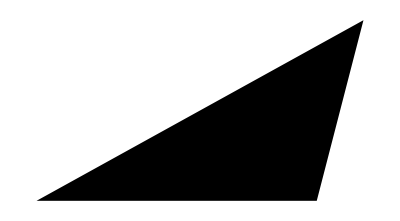

```mathematica
Block[{a=1,b=2,c=1.5},Graphics[tri]]
```

```mathematica
FullSimplify[Inequalities[tri,{x,y}],a>0&&b>0&&c>0&&(a+b-c) (a-b+c) (-a+b+c) (a+b+c)>0]
```

y≥0&&√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) x+(a^2+c^2) y≤c √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^2 y&&√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) x+a^2 y≥(b^2+c^2) y

```mathematica
ineq[x_,y_]:=y≥0&&√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) x+(a^2+c^2) y≤c √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^2 y&&√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) x+a^2 y≥(b^2+c^2) y
```

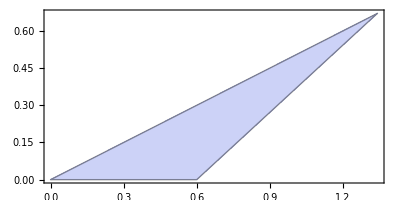

```mathematica
Block[{a=1,b=1.5,c=.6,d=.7},RegionPlot[ineq[x,y],{x,0,Max[c,(-a^2+b^2+c^2)/(2 c)]},{y,0,1/(2c) √((-a+b+c) (a+b-c) (a-b+c) (a+b+c))},AspectRatio->Automatic]]
```

### Centroid

```mathematica
1/(1/4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))Integrate[{x,y}Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0]
```

{(4 (Piecewise[{{1/8 c^2 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {(c^3 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(6 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {(c^3 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(3 (-a^2+b^2+c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/(24 c)(-a^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+3 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]))/(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c))),(4 (Piecewise[{{-((a-b-c) (a+b-c) c^3 (a-b+c) (a+b+c))/(6 (a^2-b^2-c^2)^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {-((a-b-c) (a+b-c) c^3 (a-b+c) (a+b+c))/(6 (a^2-b^2+c^2)^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/24 (4 b^2 c-c^3), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^4+2 a^2 b^2-b^4+2 a^2 c^2+2 b^2 c^2-c^4)/(24 c), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]))/(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))}

```mathematica
FullSimplify[%,a>0&&b>0&&c>0]
```

{Piecewise[{{c/2, a==b&&a+b>c}, {(2 c^3)/(3 (a^2-b^2+c^2)), a>b&&√(a^2-b^2)==c}, {(4 c^3)/(3 (-a^2+b^2+c^2)), a<b&&√(-a^2+b^2)==c}, {(-a^2+b^2+3 c^2)/(6 c), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{(2 c^3 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))/(3 (-a^2+b^2+c^2)^2), a<b&&√(-a^2+b^2)==c}, {(2 c^3 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))/(3 (a^2-b^2+c^2)^2), a>b&&√(a^2-b^2)==c}, {1/6 √(4 b^2-c^2), a==b&&a+b>c}, {(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))/(6 c), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]}

### Area

```mathematica
(area=Integrate[Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0])//Timing
```

{90.3874,Piecewise[{{1/4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {1/4 c √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {(c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {(c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 (-a^2+b^2+c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {0, True}}]}

```mathematica
Δ=1/4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c));
```

```mathematica
FullSimplify[{1/4 c √(4 b^2-c^2),Δ},a>0&&a-b==0&&c>0&&a+b-c>0]
```

{1/4 c √(4 b^2-c^2),1/4 c √(4 b^2-c^2)}

```mathematica
FullSimplify[{(c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 (a^2-b^2+c^2)),Δ},a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0&&a^2-b^2==c^2&&c>0]
```

{(b c)/2,(b c)/2}

```mathematica
FullSimplify[{(c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 (-a^2+b^2+c^2)),Δ},a>0&&a-b<0&&√(-a^2+b^2)-c==0&&b^2-a^2==c^2&&c>0]
```

{1/2 c √((b-c) (b+c)),1/2 c √((b-c) (b+c))}

### InertiaTensor

FromCycles::shdw: Symbol "FromCycles" appears in multiple contexts {"Combinatorica`", "System`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

PermutationQ::shdw: Symbol "PermutationQ" appears in multiple contexts {"Combinatorica`", "System`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

Permute::shdw: Symbol "Permute" appears in multiple contexts {"Combinatorica`", "System`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

RandomPermutation::shdw: Symbol "RandomPermutation" appears in multiple contexts {"Combinatorica`", "System`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

ToCycles::shdw: Symbol "ToCycles" appears in multiple contexts {"Combinatorica`", "System`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

#### V7

```mathematica
(i=Integrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0])//Timing
```

{193.773,{{Piecewise[{{1/12 b^3 √(a^2-b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/12 a^3 √(-a^2+b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/96 c (4 b^2-c^2)^(3/2), a>0&&a-b==0&&c>0&&a+b-c>0}, {-(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{1/8 a^2 (a^2-b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/24 b^2 (-a^2+b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]},{Piecewise[{{1/8 a^2 (a^2-b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/24 b^2 (-a^2+b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{-((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (a^2-b^2-c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {7/96 c^3 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/(96 c^2)(a^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-2 a^2 b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-4 a^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+4 b^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+7 c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]}}}

```mathematica
FullSimplify[%,a>0&&b>0&&c>0]
```

{193.773,{{Piecewise[{{1/12 b^3 √((a-b) (a+b)), a>b&&√(a^2-b^2)==c}, {1/12 a^3 √(-a^2+b^2), a<b&&√(-a^2+b^2)==c}, {1/96 c (4 b^2-c^2)^(3/2), a==b&&a+b>c}, {((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(3/2)/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{1/8 a^2 (a-b) (a+b), a<b&&√(-a^2+b^2)==c}, {1/24 b^2 (-a^2+b^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]},{Piecewise[{{1/8 a^2 (a-b) (a+b), a<b&&√(-a^2+b^2)==c}, {1/24 b^2 (-a^2+b^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{-((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (a^2-b^2-c^2)), a<b&&√(-a^2+b^2)==c}, {7/96 c^3 √(4 b^2-c^2), a==b&&a+b>c}, {((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>b&&√(a^2-b^2)==c}, {(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]}}}

...last one wrong...

#### V7 GenerateConditions -> True

```mathematica
(i=Integrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},GenerateConditions->True,Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0])//Timing
```

{206.996,{{Piecewise[{{1/12 b^3 √(a^2-b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/12 a^3 √(-a^2+b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/96 c (4 b^2-c^2)^(3/2), a>0&&a-b==0&&c>0&&a+b-c>0}, {-(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{1/8 a^2 (a^2-b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/24 b^2 (-a^2+b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]},{Piecewise[{{1/8 a^2 (a^2-b^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/24 b^2 (-a^2+b^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{-((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (a^2-b^2-c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {7/96 c^3 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/(96 c^2)(a^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-2 a^2 b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-4 a^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+4 b^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+7 c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]}}}

```mathematica
FullSimplify[i,a>0&&b>0&&c>0]
```

{{Piecewise[{{1/12 b^3 √((a-b) (a+b)), a>b&&√(a^2-b^2)==c}, {1/12 a^3 √(-a^2+b^2), a<b&&√(-a^2+b^2)==c}, {1/96 c (4 b^2-c^2)^(3/2), a==b&&a+b>c}, {((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(3/2)/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{1/8 a^2 (a-b) (a+b), a<b&&√(-a^2+b^2)==c}, {1/24 b^2 (-a^2+b^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]},{Piecewise[{{1/8 a^2 (a-b) (a+b), a<b&&√(-a^2+b^2)==c}, {1/24 b^2 (-a^2+b^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{-((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (a^2-b^2-c^2)), a<b&&√(-a^2+b^2)==c}, {7/96 c^3 √(4 b^2-c^2), a==b&&a+b>c}, {((a-b)^2 (a+b)^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>b&&√(a^2-b^2)==c}, {(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]}}

#### V8

```mathematica
(i=Integrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0])//Timing
```

{561.843,{{Piecewise[{{1/96 c (4 b^2-c^2)^(3/2), a>0&&a-b==0&&c>0&&a+b-c>0}, {-(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (a^2-b^2+c^2)^3), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (-a^2+b^2+c^2)^3), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {0, True}}],Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (a^2-b^2-c^2)^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]},{Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (a^2-b^2-c^2)^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{7/96 c^3 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (-a^2+b^2+c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/(96 c^2)(a^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-2 a^2 b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-4 a^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+4 b^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+7 c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]}}}

```mathematica
FullSimplify[i,a>0&&b>0&&c>0]
```

{{Piecewise[{{1/96 c (4 b^2-c^2)^(3/2), a==b&&a+b>c}, {((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(3/2)/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {(c^4 (-(a-b-c) (a+b-c) (a-b+c) (a+b+c))^(3/2))/(12 (a^2-b^2+c^2)^3), a>b&&√(a^2-b^2)==c}, {(c^4 (-(a-b-c) (a+b-c) (a-b+c) (a+b+c))^(3/2))/(12 (-a^2+b^2+c^2)^3), a<b&&√(-a^2+b^2)==c}, {0, True}}],Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (-a^2+b^2+c^2)^2), a<b&&√(-a^2+b^2)==c}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]},{Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (-a^2+b^2+c^2)^2), a<b&&√(-a^2+b^2)==c}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}],Piecewise[{{7/96 c^3 √(4 b^2-c^2), a==b&&a+b>c}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>b&&√(a^2-b^2)==c}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (-a^2+b^2+c^2)), a<b&&√(-a^2+b^2)==c}, {(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2), (a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))}, {0, True}}]}}

```mathematica
FullSimplify[%,(a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))||(a>b&&((√(a^2-b^2)>c&&a<b+c)||(a+b>c&&√(a^2-b^2)<c)))]
```

{{Piecewise[{{1/96 c (4 b^2-c^2)^(3/2), a==b&&a+b>c}, {((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(3/2)/(96 c^2), True}}],Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (-a^2+b^2+c^2)^2), a<b&&√(-a^2+b^2)==c}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), True}}]},{Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (-a^2+b^2+c^2)^2), a<b&&√(-a^2+b^2)==c}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>b&&√(a^2-b^2)==c}, {1/48 (-4 b^2 c^2+c^4), a==b&&a+b>c}, {-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2), True}}],Piecewise[{{7/96 c^3 √(4 b^2-c^2), a==b&&a+b>c}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>b&&√(a^2-b^2)==c}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (-a^2+b^2+c^2)), a<b&&√(-a^2+b^2)==c}, {(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2), True}}]}}

```mathematica
{{((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(3/2)/(96 c^2),-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2),-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2),(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2)}
```

```mathematica
Factor[((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4)]
```

a^4-2 a^2 b^2+b^4-4 a^2 c^2+4 b^2 c^2+7 c^4

```mathematica
(i=Integrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},GenerateConditions->True,Assumptions->a>0&&b>0&&c>0&&√((-a+b+c) (a+b-c) (a-b+c) (a+b+c))>0])//Timing
```

{500.666,{{Piecewise[{{1/96 c (4 b^2-c^2)^(3/2), a>0&&a-b==0&&c>0&&a+b-c>0}, {-(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (a^2-b^2+c^2)^3), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (-a^2+b^2+c^2)^3), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {0, True}}],Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (a^2-b^2-c^2)^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]},{Piecewise[{{((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(8 (a^2-b^2-c^2)^2), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {((a-b-c) (a+b-c) c^4 (a-b+c) (a+b+c))/(24 (a^2-b^2+c^2)^2), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {1/48 (-4 b^2 c^2+c^4), a>0&&a-b==0&&c>0&&a+b-c>0}, {(-a^6+3 a^4 b^2-3 a^2 b^4+b^6+4 a^4 c^2-4 a^2 b^2 c^2-5 a^2 c^4-3 b^2 c^4+2 c^6)/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}],Piecewise[{{7/96 c^3 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (-a^2+b^2+c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/(96 c^2)(a^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-2 a^2 b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-4 a^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+4 b^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+7 c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]}}}

```mathematica
i[[1,1]]
```

Piecewise[{{1/96 c (4 b^2-c^2)^(3/2), a>0&&a-b==0&&c>0&&a+b-c>0}, {-(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(96 c^2), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (a^2-b^2+c^2)^3), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {-(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) (a^4-2 a^2 b^2+b^4-2 a^2 c^2-2 b^2 c^2+c^4))/(12 (-a^2+b^2+c^2)^3), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {0, True}}]

```mathematica
i[[2,2]]
```

Piecewise[{{7/96 c^3 √(4 b^2-c^2), a>0&&a-b==0&&c>0&&a+b-c>0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(12 (a^2-b^2+c^2)), a>0&&b>0&&a-b>0&&√(a^2-b^2)-c==0}, {(c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(4 (-a^2+b^2+c^2)), a>0&&a-b<0&&√(-a^2+b^2)-c==0}, {1/(96 c^2)(a^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-2 a^2 b^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+b^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))-4 a^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+4 b^2 c^2 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))+7 c^4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))), (b>0&&a-b-c<0&&a-b>0&&√(a^2-b^2)-c>0&&a>0)||(b>0&&a-b>0&&√(a^2-b^2)-c<0&&a>0&&a+b-c>0)||(a-b<0&&a>0&&a+b-c>0&&√(-a^2+b^2)-c<0)||(a-b<0&&a>0&&a-b+c>0&&√(-a^2+b^2)-c>0)}, {0, True}}]

```mathematica
Block[{a=1,b=1,c=1},NIntegrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,0,Max[c,(-a^2+b^2+c^2)/(2 c)]},{y,0,1/(2c) √((-a+b+c) (a+b-c) (a-b+c) (a+b+c))}]]
```

{{0.0541266,-0.0625},{-0.0625,0.126295}}

```mathematica
Block[{a=1,b=1,c=1},i]//N
```

{{0.0541266,-0.0625},{-0.0625,0.126295}}

```mathematica
FullSimplify[i,a==b==c&&c>0]
```

{{(√3 c^4)/32,-c^4/16},{-c^4/16,(7 c^4)/(32 √3)}}

```mathematica
FullSimplify[i,a≠b&&√(a^2-b^2)≠c&&√(b^2-a^2)≠c&&a>0&&b>0&&c>0&&(a<b&&((a+b>c&&√(-a^2+b^2)<c)||(√(-a^2+b^2)>c&&a+c>b)))]
```

{{(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))^(3/2)/(96 c^2),-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2)},{-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2),(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2)}}

### RadiiOfGyration

```mathematica
FullSimplify[1/(1/4 √(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))√Tr[{{(-(a-b-c) (a+b-c) (a-b+c) (a+b+c))^(3/2)/(96 c^2),-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2)},{-((a-b-c) (a+b-c) (a-b+c) (a+b+c) (a^2-b^2-2 c^2))/(96 c^2),(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) ((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(96 c^2)}},List],a>0&&c>0&&(a+b-c) (a-b+c) (-a+b+c) (a+b+c)>0]
```

{((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(1/4)/(√6 c),(√((a^2-b^2)^2+4 (-a^2+b^2) c^2+7 c^4))/(√6 c ((a+b-c) (a-b+c) (-a+b+c) (a+b+c))^(1/4))}

### Incircle

```mathematica
FullSimplify[Incircle[Triangle[{{0,0},{c,0},{(-a^2+b^2+c^2)/(2c),(√((-a+b+c)(a-b+c)(a+b-c)(a+b+c)))/(2c)}}]],a>0&&b>0&&c>0&&(-a+b+c)(a-b+c)(a+b-c)>0]
```

Circle[{1/2 (-a+b+c),(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 (a+b+c))},1/2 √(-((a-b-c) (a+b-c) (a-b+c))/(a+b+c))]

### Circumcircle

```mathematica
FullSimplify[Circumcircle[Triangle[{{0,0},{c,0},{(-a^2+b^2+c^2)/(2c),(√((-a+b+c)(a-b+c)(a+b-c)(a+b+c)))/(2c)}}]],a>0&&b>0&&c>0&&(-a+b+c)(a-b+c)(a+b-c)>0]
```

Circle[{c/2,(c (a^2+b^2-c^2))/(2 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))},a b c √(-1/(a^4+(b^2-c^2)^2-2 a^2 (b^2+c^2)))]

## Classification tables

The first three representatives classify triangles by equal side lengths; equilateral triangles are included among isosceles triangles. The last three classify triangles by their interior angles. Marks indicate equal sides or the relevant angle. Each diagram is one representative, not a restriction on other members of its class.

```mathematica
(triangleTableVertices = Association["Equilateral" -> {{0, 0}, {2, 0}, {1, Sqrt[3]}}, "Isosceles" -> {{0, 0}, {2, 0}, {1, 2}}, "Scalene" -> {{0, 0}, {3, 0}, {1, 2}}, "Acute" -> {{0, 0}, {3, 0}, {1, 2}}, "Right" -> {{0, 0}, {3, 0}, {0, 2}}, "Obtuse" -> {{0, 0}, {3, 0}, {-1, 1}}]; triangleTableFigure[key_] := Module[{v, neutral, blue, orange, ticks, mark, c, u, w, t1, t2}, v = triangleTableVertices[key]; neutral = LightDarkSwitched[Black, White]; blue = RGBColor[1/10, 2/5, 3/4]; orange = RGBColor[4/5, 2/5, 1/10]; ticks = Function[pair, Module[{middle = Mean[pair], normal = Normalize[Reverse[pair[[2]] - pair[[1]]] {1, -1}]}, Line[{middle - normal/10, middle + normal/10}]]]; mark = Switch[key, "Equilateral", {orange, ticks /@ Partition[Append[v, First[v]], 2, 1]}, "Isosceles", {orange, ticks /@ {v[[{1, 3}]], v[[{2, 3}]]}}, "Right", {orange, Line[{{1/5, 0}, {1/5, 1/5}, {0, 1/5}}]}, "Acute" | "Obtuse", c = If[key === "Acute", 3, 1]; u = Normalize[v[[Mod[c, 3] + 1]] - v[[c]]]; w = Normalize[v[[Mod[c + 1, 3] + 1]] - v[[c]]]; t1 = ArcTan @@ u; t2 = t1 + ArcCos[u . w]; {orange, Circle[v[[c]], 1/3, {t1, t2}]}, _, {}]; Graphics[{{blue, AbsoluteThickness[2], Line[Append[v, First[v]]]}, {AbsoluteThickness[3/2], mark}, neutral, MapThread[Text[Style[#1, Italic, 15, FontFamily -> "Times"], #2 + (1/5) Normalize[#2 - Mean[v]]] & , {{"A", "B", "C"}, v}]}, BaseStyle -> {FontFamily -> "Times", neutral}]]; 
)
```

### TriangleTableEquilateral

ebox basename: TriangleTableEquilateral

```mathematica
triangleTableFigure["Equilateral"]
```

-Graphics-

### TriangleTableIsosceles

ebox basename: TriangleTableIsosceles

```mathematica
triangleTableFigure["Isosceles"]
```

-Graphics-

### TriangleTableScalene

ebox basename: TriangleTableScalene

```mathematica
triangleTableFigure["Scalene"]
```

-Graphics-

### TriangleTableAcute

ebox basename: TriangleTableAcute

```mathematica
triangleTableFigure["Acute"]
```

-Graphics-

### TriangleTableRight

ebox basename: TriangleTableRight

```mathematica
triangleTableFigure["Right"]
```

-Graphics-

### TriangleTableObtuse

ebox basename: TriangleTableObtuse

```mathematica
triangleTableFigure["Obtuse"]
```

-Graphics-